# Elliptic Curve DHEC Cryptography -Graphics-

Authored by Mark Hughes:  MarkJarrodHughes@gmail.com
Work in Progress.  Usage of graphics allowed for academic purposes.

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
prefix="Hughes_"<>Riffle[StringSplit[NotebookDirectory[],"\\"][[-2;;-1]],"_"]<>"_";
```

```mathematica
imgA=-Graphics-;
imgB=-Graphics-;
imgC=-Graphics-;
```

## Choose an elliptic curve y^2=x^3-3x+B

Elliptic Curves are usually displayed in Weierstrass form y^2==x^3+Ax+B-- to demonstrate the different forms, show a 2d plot alongside a 3D slice.

```mathematica
ECC2DPlot[z_]:=ContourPlot[{y^2== x^3-3x+z},{x,-3,5},{y,-3,3},Axes->True,GridLines->{Range[-3,6,1],Range[-3,3,1]},ContourStyle->Directive[Red,Thickness[0.01]],FrameTicksStyle->Directive[Bold,Darker[Blue],16,FontFamily->"Arial Black"]]
```

Elliptic curves are smooth curves with no cusps.  If there are crossings / cusps / etc... we can’t use it.  An example is shown below -- example will change if the function changes.  (y^2=x^3+Ax+B, 4 A^3+27 B^2≠0)

## Demonstrate Elliptic Curve Point Addition

```mathematica
Quit[];
```

```mathematica
Clear[tangentEquation,fn,x,x1,x2,y,y1,y2,a];
fn=1 y^2==1 x^3-3  x+3 ;
a=Coefficient[fn[[2]],x,1];
regCurve=ImplicitRegion[fn,{x,y}];
```

```mathematica
(* FindXfromY provides an {x,y} of a given y value -- it'll produce 1, 2, or 3 useful outputs.  Good luck with that. *)
findXfromY[yValue_]:=Flatten[{Extract[##,Position[#,_Real]],yValue}]&/@N[Solve[fn/.y->yValue,Reals]]//DeleteDuplicates
(* FindYfromX provides an {x,y} of a given x value -- it'll produce 1, or 2 outputs. Again, good luck with that. *)
findYfromX[xValue_]:=Flatten[{xValue,Extract[##,Position[#,_Real]]}]&/@N[Solve[fn/.x->xValue,Reals]]//DeleteDuplicates
(* Use Y=mX+b and Y^2=X^3-3x+3 along with two known points to find a third.*)
```

```mathematica
Module[{x3},findP3from2P[{x1_,y1_}]:={x3=((3 x1^2+1a)/(2y1))^2-2x1,-y1+((3 x1^2+1a)/(2y1))(x1-x3)}/.{y->y1,x->x1}]
Module[{x3},findP3fromP1P2[{x1_,y1_},{x2_,y2_}]:= {x3=((y2-y1)/(x2-x1))^2-x1-x2,-y1+((y2-y1)/(x2-x1))(x1-x3)}/.{y->y1,x->x1}]
findP3[{x1_,y1_},{x2_,y2_}]:=If[{x1,y1}=={x2,y2},findP3from2P[{x1,y1}],findP3fromP1P2[{x1,y1},{x2,y2}]]
```

```mathematica
cntrPlot=ContourPlot[1 y^2== 1 x^3-3x+3,{x,-2.5,5.5},{y,-11,11},Axes->False,GridLines->{Range[-3,6,1],Range[-10,10,2.5]},ContourStyle->Directive[Red,Thickness[0.01]],FrameTicksStyle->Directive[Bold,Darker[Blue],14,FontFamily->"Arial Black"]]
```

```mathematica
Clear[x1,y1,x2,y2,graphicPointsOnLine,p1,p2,p3,p4]
```

```mathematica
graphicPointsOnLine[{x1_,y1_},{x2_,y2_}]:=
Module[{p1,p2,p3,p4},
p1={x1,y1};p2={x2,y2};p3=findP3[p1,p2]{1,-1};p4=findP3[p1,p2];
Show[{cntrPlot,
Graphics[{

{Thickness[0.02],
{Opacity[0.5],Blue,InfiniteLine[{p1,p3}]},
{Blue,Line[{p1,p2,p3}]},
{Darker[Green],Line[{p3,p4}]}
},

{Opacity[1],PointSize[0.1], Red, Point[p1], Blue, Point[p2],Darker[ Green], Point[p3],Point[p4]},
{Opacity[1],White,PointSize[0.08],Point[p1],Point[p2],Point[p3],Point[p4]},
{Opacity[1],
Red,If[p1≠p2,Text[Style["P",20,Bold],p1],Text[Style["2P",20],p1]],
Blue,If[p1≠p2,{Opacity[1],Text[Style["Q",18,Bold],p2]}],
Darker[Green],Text[Style["-R",20,Bold],p3],Text[Style["R",20,Bold],p4]}
}]
},ImageSize->400]]
graphicPointsOnLine[findYfromX[-1.1][[1]],findYfromX[-1.5][[1]]]
```

```mathematica
ani2[{x_,y_},n_]:=graphicPointsOnLine[{x,y},#]&/@ NestList[findP3[{x,y},#]&,{x,y},n]
```

```mathematica
num[{x_,y_},n_]:= NestList[findP3[{x,y},#]&,{x,y},n+1][[n+2]]
```

```mathematica
findXfromY[1.1][[1]]
```

{-1.97629,1.1}

```mathematica
aliceImg=ani2[findXfromY[1.1][[1]],6][[7]]/.{"R"->"A","P"->"G","-R"->"-A"}
ptA=num[findXfromY[1.1][[1]],6]
```

{1.47184,-1.33152}

```mathematica
bobImg=ani2[findXfromY[1.1][[1]],4][[5]]/.{"R"->"B","P"->"G","-R"->"-B"}
ptB=num[findXfromY[1.1][[1]],4]
```

{2.37433,-3.04338}

```mathematica
aliceAni1=ImageCompose[#,ImageResize[imgA,100],Scaled[{.2,.2}]]&/@Flatten[{ani2[findXfromY[1.1][[1]],5],ani2[findXfromY[1.1][[1]],6][[7]]/.{"R"->"A","P"->"G","-R"->"-A"}}]
bobAni1=ImageCompose[#,ImageResize[imgB,100],Scaled[{.2,.2}]]&/@Flatten[{ani2[findXfromY[1.1][[1]],3],ani2[findXfromY[1.1][[1]],4][[5]]/.{"R"->"B","P"->"G","-R"->"-B"}}]
aliceAni2=ImageCompose[#,ImageResize[imgA,100],Scaled[{.2,.2}]]&/@Flatten[{ani2[ptB,5]/."2P"->"2B",ani2[ptB,7][[7]]/.{"R"->"S","-R"->"-S"}}]
bobAni2=ImageCompose[#,ImageResize[imgB,100],Scaled[{.2,.2}]]&/@Flatten[{ani2[ptA,3]/."2P"->"2A",ani2[ptA,7][[5]]/.{"R"->"S","-R"->"-S"}}]
```

```mathematica
Export[prefix<>"aliceAni1.gif",aliceAni1,AnimationRepetitions->Infinity,"DisplayDurations"->{1,1,1,1,1,1,5}];
Export[prefix<>"bobAni1.gif",bobAni1,AnimationRepetitions->Infinity,"DisplayDurations"->{1,1,1,1,7}];
Export[prefix<>"aliceAni2.gif",aliceAni2,AnimationRepetitions->Infinity,"DisplayDurations"->{1,1,1,1,1,1,5}];
Export[prefix<>"bobAni2.gif",bobAni2,AnimationRepetitions->Infinity,"DisplayDurations"->{1,1,1,1,7}];
```

```mathematica
Max[{Length[bobAni1],Length[aliceAni1]}]
Min[{Length[bobAni1],Length[aliceAni1]}]
```

7

5

```mathematica
If[#≤Min[{Length[bobAni1],Length[aliceAni1]}],#,Min[{Length[bobAni1],Length[aliceAni1]}]]
```

If[#1≤5,#1,Min[{Length[bobAni1],Length[aliceAni1]}]]

```mathematica
ListAnimate[ani3=GraphicsGrid[{
{aliceAni1[[#]],bobAni1[[If[#≤Min[{Length[bobAni1],Length[aliceAni1]}],#,Min[{Length[bobAni1],Length[aliceAni1]}]]]]}},ImageSize->800]&/@Range[Length[aliceAni1]]]
```

```mathematica
Export[prefix<>"AliceBobPointAdditionPartOne.gif",ani3,AnimationRepetitions->∞, "DisplayDurations"->{1,1,1,1,1,1,8}]
```

Hughes_TechnicalArticles_EllipticCurveCryptography_AliceBobPointAdditionPartOne.gif

```mathematica
ListAnimate[ani4=GraphicsGrid[{
{aliceAni2[[#]],bobAni2[[If[#≤Min[{Length[bobAni2],Length[aliceAni2]}],#,Min[{Length[bobAni2],Length[aliceAni2]}]]]]}},ImageSize->800]&/@Range[Length[aliceAni2]]]
```

```mathematica
Export[prefix<>"AliceBobPointAdditionCombined.gif",Flatten[{ani3,ani4}],AnimationRepetitions->∞, "DisplayDurations"->{1,1,1,1,1,1,3,1,1,1,1,1,1,5}]
```

Hughes_TechnicalArticles_EllipticCurveCryptography_AliceBobPointAdditionCombined.gif

```mathematica
Export[prefix<>"AliceBobPointAdditionPartTwo.gif",ani4,AnimationRepetitions->∞, "DisplayDurations"->{1,1,1,1,1,1,8}]
```

Hughes_TechnicalArticles_EllipticCurveCryptography_AliceBobPointAdditionPartTwo.gif

```mathematica
Clear[lista,listb]
```

```mathematica
lista=Table[num[ptA,n],{n,1,25}]
listb=Table[num[ptB,n],{n,1,25}]
```

{{-0.149731,1.8563},{2.54258,3.43648},{15.8146,-62.5363},{0.923474,-1.00852},{-2.04837,-0.741939},{0.604586,1.18627},{6.352,15.4995},{4.07081,-7.63197},{0.334146,-1.42649},{-1.79902,1.60455},{1.13295,1.02731},{45.8429,310.173},{1.97205,-2.18016},{-0.565527,-2.12502},{-0.754622,2.19867},{1.79678,1.84674},{92.3987,-888.021},{1.22472,-1.07835},{-1.64703,-1.86365},{0.204298,1.54778},{3.48387,5.90198},{7.9692,-22.0273},{0.704831,-1.1116},{-2.09446,0.308984},{0.834223,1.03822}}

{{-2.00341,-0.984498},{-0.149731,1.8563},{1.54361,1.4308},{25.0901,125.389},{4.50175,-8.98476},{0.923474,-1.00852},{-1.33074,-2.15306},{-0.985845,2.23593},{1.08,1.00981},{6.352,15.4995},{13.0055,-46.5162},{1.34174,-1.17909},{-0.456449,-2.06743},{-1.79902,1.60455},{0.665057,1.13973},{2.94991,4.45199},{164.257,-2105.04},{1.97205,-2.18016},{0.258108,-1.49762},{-2.09891,-0.224018},{0.121821,1.62368},{1.79678,1.84674},{67.5197,554.633},{3.38772,-5.63174},{0.761688,-1.07557}}

```mathematica
num[ptA,4]
num[ptB,6]
num[ptA,10]
num[ptB,14]
```

{0.923474,-1.00852}

{0.923474,-1.00852}

{-1.79902,1.60455}

{-1.79902,1.60455}

```mathematica
bobImg2=ani2[ptA,4][[5]]/.{"R"->"S","P"->"B"}
aliceImg2=ani2[ptB,6][[7]]/.{"R"->"S","P"->"A"}
```

```mathematica
Clear[img]
img[n_]:=img[n]=Module[{a,b,A,B,g,p},
g=RandomInteger[{2^7,2^8}];
p=NextPrime[g];
a=RandomInteger[{150,280}];
b=RandomInteger[{150,280}];
B=Mod[g^b,p];
A=Mod[g^a,p];
Grid[
{
{"",Style["Good Guys",Bold,Purple,36],SpanFromLeft,Style["Bad Guy",Bold,Darker[Green],36]},
{"",imgA,imgB,imgC},
{"",Style["Alice",Red,Bold,24],Style["Bob",Blue,Bold,24],Style["Eve",Darker[Green],Bold,24]},
{"Alice and Bob agree on\ncurve parameters and\nstarting point G",Style["p,a,b,G,n,h",20],SpanFromLeft,Style["p,a,b,G,n,h",20]},
{"Alice and Bob pick\nrandom integer\nsecrets α and β",Style["α="<>ToString[a],20],Style["β="<>ToString[b],20],""},
{"Alice and Bob multiply\nthe point G by their\nsecret number to\nfind points\nA=αG, B=βG",aliceImg,bobImg,""},
{"Alice and Bob transmit\npoints A and B",Style["B",20],Style["A",20],Style["A,B",20]},
{"Alice and Bob multiply\nthe points B, A by their\nsecret numbers to\nfind point S\nthe shared secret",aliceImg2/."A"->"B",bobImg2/."B"->"A",""}

},Dividers->{{False,False,False,True,False},{False,False,False,True,True,True,True,True,True,True}},Alignment->{Center,Center}
]]
img[1]
```

```mathematica
Export[prefix<>"AliceBob_DHEC_complete.jpg",img[1],ImageSize->800]
```

Hughes_TechnicalArticles_EllipticCurveCryptography_AliceBob_DHEC_complete.jpg

```mathematica
Directory[]
```

D:\Dropbox\AllAboutCircuits\TechnicalArticles\EllipticCurveCryptography

## Find elliptic curve plot points

Pick an Elliptic Curve to use

```mathematica
PrimeQ[q=281] (* Max Value of Dataset *)
fn = y^2-(x^3-3x+0); (* Elliptic Curve *)
Grid[Partition[data=RotateLeft[Flatten[Drop[Reap[
Table[
If[
Mod[fn,q]==0,Sow[{x,y}]],(* Only collect where fn = 0 *)
{x,0,q-1},
{y,0,q-1}];
],1],2]],8]](* Remove some extra parenthesis.  Move (0,0) to end to better demonstrate symmetry.  Also, drop a few datapoints to make the table easy to read.  *)
```

True

```mathematica
Grid[Partition[reducedData=DeleteDuplicates[RotateRight[data]/.{x_,y_}->{x,q/2.±Abs[(y-q/2.)]}],5]]; (* Probably not going to use this version*)
```

```mathematica
Grid[Partition[Options[Grid],5]]
```

Alignment→{Center,Baseline} | AllowedDimensions→Automatic | AllowScriptLevelChange→True | AutoDelete→False | Background→None
BaselinePosition→Automatic | BaseStyle→{} | DefaultBaseStyle→Grid | DefaultElement→□ | DeleteWithContents→True
Dividers→{} | Editable→Automatic | Frame→None | FrameStyle→Automatic | ItemSize→Automatic

```mathematica
imgData=Grid[Partition[Row[{Style["●",22,Bold,ColorData[2][Abs[Round[140.5-(#[[2]])/1.,1]]]],Style["("<>ToString[#[[1]]]<>", "<>ToString[#[[2]]]<>")",22,Bold,Background->White]}]&/@data,8],Alignment->Left]
```

```mathematica
Export[prefix<>"DataPointColoring.jpg",imgData,ImageSize->1200]
```

Hughes_TechnicalArticles_EllipticCurveCryptography_DataPointColoring.jpg

```mathematica
Length[reducedData]//Divisors
```

{1,5,25,125}

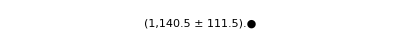
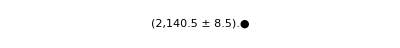
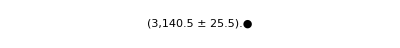
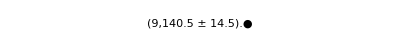
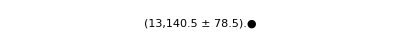
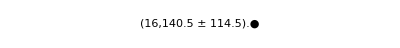
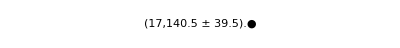
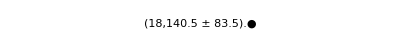
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
imgReducedData=Grid[Partition[Graphics[{
Text[
Style["("<>ToString[#[[1]]]<>","<>ToString[#[[2]]]<>")",18]
.
Style["●",18,ColorData[2][Abs[Round[140.5-(#[[2,2]])/1.,1]]]]]
},AspectRatio->1/10]&/@reducedData,5],ItemSize->Full]
```

```mathematica
img1ListPlot=ListPlot[Style[#, ColorData[2][Abs[Round[140.5-(#[[2]])/1.,1]]]] & /@ Sort[data,#1[[2]]<#2[[2]]&],AspectRatio->1,PlotStyle->PointSize[0.02],PlotRange->{{-1,q+1},{-1,q+1}},GridLines->{{},{{q/2,Directive[Red,Dashed,Thickness[0.01]]}}},TicksStyle->Directive[Blue, Thick, Italic,32], ImageSize->800]
```

```mathematica
Export[prefix<>"DatapointsOnGraph_colored.jpg",img1ListPlot,ImageSize->800]
```

Hughes_TechnicalArticles_EllipticCurveCryptography_DatapointsOnGraph_colored.jpg

```mathematica
img2ListPlot=ListPlot[Style[#, ColorData[2][Abs[Round[140.5-(#[[2]])/1.,1]]]] & /@ Sort[data,#1[[2]]<#2[[2]]&],AspectRatio->1,PlotStyle->PointSize[0.02],PlotRange->{{-0.1,q+0.1},{-0.1,q+.1}},GridLines->{{
{q,Directive[Thickness[0.01],Dashed,Darker[Purple]]},
{q/2.,Directive[Darker[Green],Dashed,Thickness[0.01]]},
{0,Directive[Thickness[0.01],Dashed,Darker[Purple]]}
},
{{0,Directive[Blue,Dashed,Thickness[0.01]]},
{q/2,Directive[Red,Dashed,Thickness[0.01]]},
{q,Directive[Blue,Dashed,Thickness[0.01]]}}
},TicksStyle->None,Axes->None,Frame->None, ImageSize->800]
```

```mathematica
(* Equation to map points onto surface of torus *)
```

```mathematica
With[{R = 3, r = 1.2}, torus[{u_, v_}] := {(R + r*Cos[2 Pi u])*Cos[2 Pi v], (R + r*Cos[2 Pi u])*Sin[2 Pi v], r*Sin[2 Pi u]}]
```

Equation modified to change the direction of data wrapping around the torus -- makes it easier for readers to see.  The  selection of the location of points on the torus is arbitrary.  Best to make it useful for the reader.

```mathematica
With[{R = 3, r = 1.2}, torus[{v_, u_}] := {(R + r*Cos[2.π u+π])*Cos[2. π v], (R + r*Cos[2. π u+π])*Sin[2. π v], r*Sin[2 π u+π]}]
```

```mathematica
(* Sanity Check -- should show symmetry like a seeded bagel *)
```

```mathematica
Show[{Graphics3D[{PointSize[0.02],ColorData[2][Abs[Round[q/2.-(#[[2]])/1.,1]]],
Point[torus[#/q]]
}]&/@ data}]
```

```mathematica
img1ToroidPlot=Show[{
ParametricPlot3D[torus[{u,v}],{u,0,1},{v,0,1},PlotStyle->Directive[Opacity[.8],White],Mesh->None],
Graphics3D[{Dashed,Thickness[0.005],Blue,Line[torus[{#,0}]&/@Range[0,1,0.01]],Red,Line[torus[{#,0.5}]&/@Range[0,1,0.01]]}],
Graphics3D[{Dashed,Thickness[0.005],Darker[Purple],Line[torus[{0,#}]&/@Range[0,1,0.01]],Darker[Green],Line[torus[{0.5,#}]&/@Range[0,1,0.01]]}],
Graphics3D[{PointSize[0.02],ColorData[2][Abs[Round[140.5-(#[[2]])/1.,1]]],
Sphere[torus[#/q],0.08]}]&/@ Sort[data,#1[[2]]<#2[[2]]&]},Boxed->False,Axes->False,ViewAngle->Pi/10.,ViewVertical->{0, 0, 1},ViewCenter->{0.5, 0.5, 0.5},ViewPoint->{0, 3.,1.2},(*Lighting->{{"Point", White, {0, 1, 4}}},LightingAngle->{0,Pi/12},*)ImageSize->800]
```

```mathematica
img1Combined=GraphicsGrid[{{img2ListPlot,img1ToroidPlot}},ImageSize->800]
```

```mathematica
Export[prefix<>"TorusWithPoints_colored.jpg",img1Combined]
```

Hughes_TechnicalArticles_EllipticCurveCryptography_TorusWithPoints_colored.jpg

```mathematica
pt1 := data[[RandomInteger[Length[data]]]]
pt2 := data[[RandomInteger[Length[data]]]]
```

```mathematica
pt1s={235,204} (* 235, 204 *)
pt2s={187,89} (* 187, 89 *)
m=1.(pt2s[[2]]-pt1s[[2]])/(pt2s[[1]]-pt1s [[1]])
```

{235,204}

{187,89}

2.39583

```mathematica
{eqM, eqB} = Extract[Normal[LinearModelFit[{pt1s, pt2s}, x, x]], {{2, 1}, {1}}]
eqTot = eqM x + eqB
```

{2.39583,-359.021}

-359.021+2.39583 x

```mathematica
img2ListPlot=
Show[{
ListPlot[Style[#, ColorData[2][Abs[Round[140.5-(#[[2]])/1.,1]]]] & /@ Sort[data,#1[[2]]<#2[[2]]&],AspectRatio->1,PlotRange->{{-1,q+1},{-1,q+1}},GridLines->{{{q,Directive[Thickness[0.005],Dashed,Darker[Purple]]},{q/2.,Directive[Darker[Green],Dashed,Thickness[0.005]]}},{0,{q/2,Directive[Red,Dashed,Thickness[0.005]]},{q,Directive[Blue,Dashed,Thickness[0.005]]}}},TicksStyle->Directive[Blue, Thick, Italic,28], ImageSize->800],
Graphics[{Blue,Thickness[0.01],InfiniteLine[{pt1s,pt2s}],InfiniteLine[{pt1s+{q/eqM,0},pt2s+{q/eqM,0}}],InfiniteLine[{pt1s+-2{q/eqM,0},pt2s+-2{q/eqM,0}}],InfiniteLine[{pt1s+-{q/eqM,0},pt2s+-{q/eqM,0}}]}]
}]
img2ToroidPlot=Show[{
ParametricPlot3D[torus[{u,v}],{u,0,1},{v,0,1},PlotStyle->Directive[Opacity[.8],White],Mesh->None],
Graphics3D[{Thickness[0.01],Blue,Line[torus[{#,eqTot/.x->#}/q]&/@Range[0q,1q,.1]]}],
Graphics3D[{Dashed,Thickness[0.005],Blue,Line[torus[{#,0}]&/@Range[0,1,0.01]],Red,Line[torus[{#,0.5}]&/@Range[0,1,0.01]]}],
Graphics3D[{Dashed,Thickness[0.005],Darker[Purple],Line[torus[{0,#}]&/@Range[0,1,0.01]],Darker[Green],Line[torus[{0.5,#}]&/@Range[0,1,0.01]]}],
Graphics3D[{PointSize[0.02],ColorData[2][Abs[Round[140.5-(#[[2]])/1.,1]]],
Sphere[torus[#/q],0.08]}]&/@ Sort[data,#1[[2]]<#2[[2]]&]},Boxed->False,Axes->False,ViewAngle->Pi/10.,ViewVertical->{0, 0, 1},ViewCenter->{0.5, 0.5, 0.5},ViewPoint->{0, 3.,1.2},(*Lighting->{{"Point", White, {0, 1, 4}}},LightingAngle->{0,Pi/12},*)ImageSize->800]
```

```mathematica
img2Combined=GraphicsGrid[{{img2ListPlot,img2ToroidPlot}},ImageSize->1200]
```

```mathematica
Export[prefix<>"TorusWithPointsAndLine_colored.jpg",img2Combined]
```

Hughes_TechnicalArticles_EllipticCurveCryptography_TorusWithPointsAndLine_colored.jpg

```mathematica
fn
```

y^2==3-3 x+x^3

```mathematica
PrimeQ[q=281] (* Max Value of Dataset *)
fn = y^2-(x^3-3x+0); (* Elliptic Curve *)
Grid[Partition[data=RotateLeft[Flatten[Drop[Reap[
Table[
If[
Mod[fn,q]==0,Sow[{x,y}]],(* Only collect where fn = 0 *)
{x,0,q-1},
{y,0,q-1}];
],1],2]],8]]
```

True